```mathematica
DSolve[{
TB'[t]==-U*A*(TB[t]-TW[t])/(mB*cpB),
TW'[t]==U*A*(TB[t]-TW[t])/(mW*cpW),
TB[0]==TB0,
TW[0]==TW0 },{TB[t],TW[t]},t]
```

{{TB[t]→(cpB mB TB0+cpW ⅇ^((A (-cpB mB-cpW mW) t U)/(cpB cpW mB mW)) mW TB0+cpW mW TW0-cpW ⅇ^((A (-cpB mB-cpW mW) t U)/(cpB cpW mB mW)) mW TW0)/(cpB mB+cpW mW),TW[t]→-(-cpB mB TB0+cpB ⅇ^((A (-cpB mB-cpW mW) t U)/(cpB cpW mB mW)) mB TB0-cpB ⅇ^((A (-cpB mB-cpW mW) t U)/(cpB cpW mB mW)) mB TW0-cpW mW TW0)/(cpB mB+cpW mW)}}

```mathematica
U=1000;
A = 9 / 10000;
cpB = 10;
cpW = 4.184;
TW0 = 0;
TB0 = 323;
mB = 5;
mW = 1000;
```

```mathematica
TB[t_]:=(cpB*mB*TB0+cpW*mW*TW0+(TB0 - TW0)*cpW*mW *Exp[(-cpB*mB-cpW*mW)*t*U*A /(cpB*cpW*mB*mW)])/(cpB*mB+cpW*mW);
```

```mathematica
TW[t_]:=(cpB*mB*TB0+cpW*mW*TW0-(TB0-TW0)*cpB*mB*Exp[(-cpB*mB-cpW*mW)*t*U*A /(cpB*cpW*mB*mW)])/(cpB*mB+cpW*mW);
```

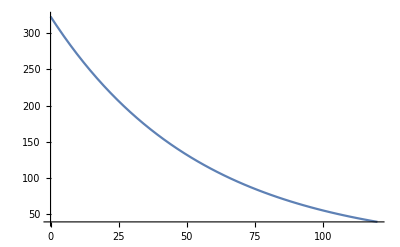

```mathematica
Plot[TB[t],{t,0,120},PlotRange->All]
```

```mathematica
(*the alternate equation below assumes that the temperature of the water does not change with time*)
```

```mathematica
TB2[t_]:=TW0+(TB0-TW0)*Exp[-U*A*t/(mB*cpB)];
```

```mathematica
Q[t]=(TB0-TB2[t])*cpB*mB
```

cpB mB (TB0-ⅇ^(-(A t U)/(cpB mB)) (TB0-TW0)-TW0)

```mathematica
iceMelted = Q[t] / (γF * mIce)
```

(cpB mB (TB0-ⅇ^(-(A t U)/(cpB mB)) (TB0-TW0)-TW0))/(mIce γF)